```mathematica
Clear[val]
setLCaCb[θ_] := Module[{R, toLCaCb, fromLCaCb}, 
      toLCaCb = Function[{val}, "rrR" . val*{1/Sqrt[3], Sqrt[3/8], 1/Sqrt[2]} + {0, 0.5, 0.5}] /. {"rrR" -> Simplify[LCaCb[-θ]]}; 
    fromLCaCb = Function[{val}, "iR" . ((val - {0, 0.5, 0.5})*{Sqrt[3], 2*Sqrt[2/3], Sqrt[2]})] /. {"iR" -> iLCaCb[-θ]};
 {toLCaCb, fromLCaCb}]
```

```mathematica
setLCaCb[LCaCbθ]
```

{Function[{val},{{1/(√3),1/(√3),1/(√3)},{0.30208,0.505893,-0.807973},{-0.758561,0.640889,0.117671}}.val {1/(√3),√(3/8),1/(√2)}+{0,0.5,0.5}],Function[{val},{{1/(√3),0.30208,-0.758561},{1/(√3),0.505893,0.640889},{1/(√3),-0.807973,0.117671}}.((val-{0,0.5,0.5}) {√3,2 √(2/3),√2})]}

```mathematica
MatrixForm[N@LCaCb[-LCaCbθ]]
MatrixForm[Simplify[RotationMatrix[LCaCbθ,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[Pi/4,{0,1,0}]]]
```

(0.57735 | 0.57735 | 0.57735
0.30208 | 0.505893 | -0.807973
-0.758561 | 0.640889 | 0.117671)

(0.57735 | 0.57735 | 0.57735
0.30208 | 0.505893 | -0.807973
-0.758561 | 0.640889 | 0.117671)

```mathematica
MatrixForm[N@iLCaCb[-LCaCbθ]]
MatrixForm[Simplify[Inverse[RotationMatrix[LCaCbθ,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[Pi/4,{0,1,0}]]]]
```

(0.57735 | 0.30208 | -0.758561
0.57735 | 0.505893 | 0.640889
0.57735 | -0.807973 | 0.117671)

(0.57735 | 0.30208 | -0.758561
0.57735 | 0.505893 | 0.640889
0.57735 | -0.807973 | 0.117671)

```mathematica
Clear[WOBOPathLCaCb]
WOBOPathLCaCb[rgb:{_,_,_},scale_:1,θ_]:=Module[{ordering,sca,a,b,c,toLCaCb, fromLCaCb},
{toLCaCb, fromLCaCb}=setLCaCb[θ];
sc=N[1/128];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
scale {
toLCaCb[{0,0,0}],
toLCaCb[ReplacePart[rgb-b,{ordering[[1]]->0,ordering[[2]]->0}]],
toLCaCb[(rgb-a)],
toLCaCb[(rgb+(1-c))],
toLCaCb[(ReplacePart[rgb+(1-b),{ordering[[3]]->1,ordering[[2]]->1}])],
toLCaCb[({1,1,1})]}
]
```

## The Final Values

```mathematica
sig=1;
```

```mathematica
1<=sig<=2.5
LCaCbθ=0.902576829326826; 
Θ=Quotient[LCaCbθ,Pi/6]Pi/6;
δθ=Mod[LCaCbθ,Pi/6];
c = {127.5,90.92186223027412,122.09591414487721};
s = {255 uG[γMin/2],sig  6.655674357484659,sig 2.934431559612464};
```

1≤sig≤2.5

```mathematica
c
```

{127.5,90.9219,122.096}

```mathematica
s
```

{765.,6.65567,2.93443}

```mathematica
csParam=colorSpaceParams[s,c,LCaCbθ,8,{{{0,0,0},{255,255,255}},{{0,0,0},{255,255,255}}},Unit->False,G->False] ;
TableForm[csParam]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

μ→{0.5,0.356556,0.478808}
c→{127.5,90.9219,122.096}
σ→{3.,0.0261007,0.0115076}
s→{765.,6.65567,2.93443}
γ→{0.235702,27.0915,61.4471}
g→{0.000924323,0.106241,0.240969}
sMin→{0,0,0}
sMax→{255,255,255}
dMin→{0,0,0}
dMax→{255,255,255}
sRange→{255,255,255}
dRange→{255,255,255}
K→{1,1,1}
δ→{1.00463,15.2847,34.6678}
m→{1.00463,15.2847,34.6678}
ω→{{0.211592,0.788408},{0.295603,0.41751},{0.448163,0.509452}}
Ω→{{53.956,201.044},{75.3787,106.465},{114.281,129.91}}
ωp→{{0.00395765,0.996042},{0.287161,0.425951},{0.448212,0.509403}}
Ωp→{{1.0092,253.991},{73.2261,108.618},{114.294,129.898}}
λ→{{0.00395765,0.996042},{0.287161,0.425951},{0.448212,0.509403}}
Λ→{{1.0092,253.991},{73.2261,108.618},{114.294,129.898}}
dis→{Function[{x$},963.226 (0.132368+Erf[0.000924323 (-127.5+x$)]),Listable],Function[{x$},127.5 (1.+Erf[0.106241 (-90.9219+x$)]),Listable],Function[{x$},127.5 (1.+Erf[0.240969 (-122.096+x$)]),Listable]}
θ→0.902577
δqS→{{0,0,0},{0,1,1},{1,1,0}}
L→{√3,1.61595,1.51712}
κ→{0.99539,0.618833,0.659143}
tRange→{1.00463,1.61595,1.51712}
λRGB2→{1.,0.883894,0.879673}
mp→{0.,0.883894,1.}
αβ→{0.,3.03424,2.85665}
α→3.03424
β→2.85665
τ→1/3
LCaCbColor→LCaCbColor$148226
qRsMin→{0,-16320,-16320}
qRsMax→{0,16320,16320}
qRsRange→{768,32640,32640}
Λq→{{3,765},{9373,13903},{14630,16627}}
Ωpq→{{3,765},{9373,13903},{14630,16627}}
Qdisc→{False,True,True}
Qdist→{False,False,False}
Qkeep→{True,True,True}
S→{0.334877,0.0126246,0.0118525}
disFun→{Function[{x$},0.334877 x$],Function[{x$},Piecewise[{{0, x$≤9373}, {0.0126246 (-9373+x$), 9373<x$<13903}, {57.1893, 13903≤x$}, {0, True}}]],Function[{x$},Piecewise[{{0, x$≤14630}, {0.0118525 (-14630+x$), 14630<x$<16627}, {23.6695, 16627≤x$}, {0, True}}]]}
dstMax→{257,57,24}
qR→{{1,1,1},{64,-40,-24},{-10,-54,64}}
fS→{1,-1,1}

```mathematica
colorSpaceRules=colorSpaceParams[s,c,LCaCbθ,8,{{{0,0,0},{255,255,255}},{{0,0,0},{255,255,255}}},Unit->False,G->False];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

```mathematica
colorSpaceRules
```

{μ→{0.5,0.356556,0.478808},c→{127.5,90.9219,122.096},σ→{3.,0.0261007,0.0115076},s→{765.,6.65567,2.93443},γ→{0.235702,27.0915,61.4471},g→{0.000924323,0.106241,0.240969},sMin→{0,0,0},sMax→{255,255,255},dMin→{0,0,0},dMax→{255,255,255},sRange→{255,255,255},dRange→{255,255,255},K→{1,1,1},δ→{1.00463,15.2847,34.6678},m→{1.00463,15.2847,34.6678},ω→{{0.211592,0.788408},{0.295603,0.41751},{0.448163,0.509452}},Ω→{{53.956,201.044},{75.3787,106.465},{114.281,129.91}},ωp→{{0.00395765,0.996042},{0.287161,0.425951},{0.448212,0.509403}},Ωp→{{1.0092,253.991},{73.2261,108.618},{114.294,129.898}},λ→{{0.00395765,0.996042},{0.287161,0.425951},{0.448212,0.509403}},Λ→{{1.0092,253.991},{73.2261,108.618},{114.294,129.898}},dis→{Function[{x$},963.226 (0.132368+Erf[0.000924323 (-127.5+x$)]),Listable],Function[{x$},127.5 (1.+Erf[0.106241 (-90.9219+x$)]),Listable],Function[{x$},127.5 (1.+Erf[0.240969 (-122.096+x$)]),Listable]},θ→0.902577,δqS→{{0,0,0},{0,1,1},{1,1,0}},L→{√3,1.61595,1.51712},κ→{0.99539,0.618833,0.659143},tRange→{1.00463,1.61595,1.51712},Hold[λRGB2$142059[0.902577,{{0.00395765,0.996042},{0.287161,0.425951},{0.448212,0.509403}}]],mp→mp$142059,αβ→αβ$142059,α→α$142059,β→β$142059,τ→τ$142059,LCaCbColor→LCaCbColor$142059,qRsMin→qRsMin$142059,qRsMax→qRsMax$142059,qRsRange→qRsRange$142059,Λq→Λq$142059,Ωpq→Ωpq$142059,Qdisc→Qdisc$142059,Qdist→Qdist$142059,Qkeep→Qkeep$142059,S→S$142059,disFun→disFun$142059,dstMax→dstMax$142059,qR→qRval$142059,fS→fS$142059}

```mathematica
colorSpaceRules/.{Rule[sym_,val_]:> sym}
```

{μ,c,σ,s,γ,g,sMin,sMax,dMin,dMax,sRange,dRange,K,δ,m,ω,Ω,ωp,Ωp,λ,Λ,dis,θ,δqS,L,κ,tRange,λRGB2,mp,αβ,α,β,τ,LCaCbColor,qRsMin,qRsMax,qRsRange,Λq,Ωpq,Qdisc,Qdist,Qkeep,S,disFun,dstMax,qR,fS}

```mathematica
{μ,c,σ,s,γ,g,sMin,sMax,dMin,dMax,sRange,dRange,K,δ,m,ω,Ω,ωp,Ωp,λ,Λ,dis,qRsMin,qRsMax,qRsRange,Λq,Ωpq,Qdisc,Qdist,Qkeep,S,disFun,dstMax,qR,fS}={"μ","c","σ","s","γ","g","sMin","sMax","dMin","dMax","sRange","dRange","K","δ","m","ω","Ω","ωp","Ωp","λ","Λ","dis","qRsMin","qRsMax","qRsRange","Λq","Ωpq","Qdisc","Qdist","Qkeep","S","disFun","dstMax","qR","fS"}
```

```mathematica
{μ,c,σ,s,γ,g,sMin,sMax,dMin,dMax,sRange,dRange,K,δ,m,ω,Ω,ωp,Ωp,λ,Λ,dis,qRsMin,qRsMax,qRsRange,Λq,Ωpq,Qdisc,Qdist,Qkeep,S,disFun,dstMax}= {"μ","c","σ","s","γ","g","sMin","sMax","dMin","dMax","sRange","dRange","K","δ","m","ω","Ω","ωp","Ωp","λ","Λ","dis","qRsMin","qRsMax","qRsRange","Λq","Ωpq","Qdisc","Qdist","Qkeep","S","disFun","dstMax"}/.colorSpaceRules;
```

```mathematica
Clear["θ","δqS","L","sRange","dRange","K","δ","λ","Λ","ω","Ω","ωp","Ωp","κ","tRange","λRGB2","mp","αβ","α","β","τ","LCaCbColor","qRsMin","qRsMax","qRsRange","Λq","Ωpq","Qdisc","Qdist","Qkeep","S","disFun","dstMax"]
```

```mathematica
colorSpaceRules/.{Rule[sym_,val_]:> Set[Symbol[sym],val]}
```

Set::write: Tag Symbol in Symbol["\[Theta]"] is Protected.

Set::write: Tag Symbol in Symbol["\[Delta]qS"] is Protected.

Set::write: Tag Symbol in Symbol["L"] is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

```mathematica
Block[{n=8,δ,K,L,λ,ωp,qRsMin,qRsRange,Λ,Ωp,Λq,Ωpq},
δ=("δ"/.distroRules);
K=("K"/.distroRules);
L="L"/.distroRules;
λ="λ"/.distroRules;
ωp="ωp"/.distroRules;
qRsMin={0,-2^(2n-1),-2^(2n-1)};
qRsRange={(2^(n+2)),2^(2n),2^(2n)};
Λ=Round[2^n λ]; Λq=Round[qRsRange λ];
Ωp=Round[2^n λ]; Ωpq=Round[qRsRange λ];


Column[{
Row[{"S = ",MatrixForm[MapThread[Min,{δ K,N[L]}] {1/3,2^(1-n),2^(1-n)}]}],
Row[{2^n Subscript["Q", "discard"]," = ",MatrixForm[Round[2^n ({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "distribute"]," = ",MatrixForm[Round[2^n(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "keep"]," = ",MatrixForm[Round[2^n(ωp[[All,2]]-ωp[[All,1]])]]}],
Row[{ Subscript["τ", "discard"]," = ",2^3/2^n}],
Row[{Subscript["τ", "distribute"]," = ",2^3/2^n}],
Row[{Subscript["τ", "keep"]," = ",1/2^n}],
Row[{ Subscript["Q", "discard"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{Subscript["Q", "distribute"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{Subscript["Q", "keep"]," = ",MatrixForm[Map[(Row[{1/2^n," < ",#}] )&,(ωp[[All,2]]-ωp[[All,1]])]]," = ",MatrixForm[Map[(1/2^n<#)&,(ωp[[All,2]]-ωp[[All,1]])]]}],
Grid[{{"","0-1","0-255","qRange"},{"λ",MatrixForm@λ,MatrixForm@Λ,MatrixForm@Λq},{"ω",MatrixForm@ωp,MatrixForm@Ωp,MatrixForm@Ωpq}}]
}]
]
```

S = (0.334877
0.0126246
0.0118525)
256 Q_discard = (2
220
240)
256 Q_distribute = (0
0
0)
256 Q_keep = (254
36
16)
τ_discard = 1/32
τ_distribute = 1/32
τ_keep = 1/256
Q_discard = (1/32 < 0.0079153
1/32 < 0.86121
1/32 < 0.938808) = (False
True
True)
Q_distribute = (1/32 < 0.
1/32 < 0.
1/32 < 0.) = (False
False
False)
Q_keep = (1/256 < 0.992085
1/256 < 0.13879
1/256 < 0.0611915) = (True
True
True)
 | 0-1 | 0-255 | qRange
λ | (0.00395765 | 0.996042
0.287161 | 0.425951
0.448212 | 0.509403) | (1 | 255
74 | 109
115 | 130) | (4 | 1020
18819 | 27915
29374 | 33384)
ω | (0.00395765 | 0.996042
0.287161 | 0.425951
0.448212 | 0.509403) | (1 | 255
74 | 109
115 | 130) | (4 | 1020
18819 | 27915
29374 | 33384)

```mathematica
qRsRange
```

{1024,65536,65536}

```mathematica
(ωp[[All,2]]-ωp[[All,1]])
```

{0.992085,0.13879,0.0611915}

```mathematica
"tRange"/.distroRules
```

{1.00463,1.61595,1.51712}

```mathematica
N[1/255]
```

0.00392157

```mathematica
"λ"/.distroRules
```

{{0.00395765,0.996042},{0.287161,0.425951},{0.448212,0.509403}}

```mathematica
Grid[{{Row[{"θ = ",Θ+δθ," ≃ ",(2 π)/7}],SpanFromLeft,SpanFromLeft},{TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ","θ"," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA[47,8],Θ +thetaExtremaB[43,8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA[49,8],Θ +thetaExtremaB[45,8]}]}]]
}},Spacings->2,Frame->All,Alignment->Left]
```

θ = 0.902577 ≃ (2 π)/7 |  | 
(ϕ^o)_a(TraditionalForm`"47", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"43", TraditionalForm`8)+π/6 < θ < (ϕ^o)_a(TraditionalForm`"49", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"45", TraditionalForm`8)+π/6 | (ϕ^o)_a(TraditionalForm`"47", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"43", TraditionalForm`8)+π/6 < (2 π)/7 < (ϕ^o)_a(TraditionalForm`"49", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"45", TraditionalForm`8)+π/6 | π/6+tan^-1((47 √3)/209)
π/6+tan^-1(43/(64 √3)) < (2 π)/7 < π/6+tan^-1(49/(69 √3))
π/6+tan^-1((15 √3)/64)

```mathematica
Row[{qR["2 π"]," = ",MatrixForm[qR[(2 π)/7]]}]
Row[{fSs["2 π"]," = ",MatrixForm[fSs[(2 π)/7]]}]
```

qR[2 π] = (1 | 1 | 1
64 | -40 | -24
-10 | -54 | 64)

fSs[2 π] = (1
-1
1)

```mathematica
{N[Pi/6+thetaExtremaA[47,8]],
N[Pi/6+thetaExtremaA[49,8]]}
{N[Pi/6+thetaExtremaB[43,8]],
N[Pi/6+thetaExtremaB[45,8]]}
```

{0.895024,0.912698}

{0.893637,0.909223}

```mathematica
N[(2 π)/7]
```

```mathematica
Binarize
```

```mathematica
NumberForm[BaseForm[64* 255,2],15,DigitBlock->4,NumberSigns->{"-","+ "},NumberPadding->{"0","0"},SignPadding->True]
```

(+ 011,1111,1100,0000)_2

## Image Rotations

#### Set the final values with sig 1 .. 5

```mathematica
Clear[colorSpaceRules];
Block[{LCaCbθ,Θ,δθ,c,s},
LCaCbθ=0.902576829326826; 
Θ=Quotient[LCaCbθ,Pi/6]Pi/6;
δθ=Mod[LCaCbθ,Pi/6];
c = {127.5,90.92186223027412,122.09591414487721};
colorSpaceRules=Table[
s = {255 uG[γMin/2],sig  6.655674357484659,sig 2.934431559612464};
colorSpaceParams[ s,c,LCaCbθ,8,{{{0,0,0},{255,255,255}},{{0,0,0},{255,255,255}}},Unit->False,G->False],{sig,1,5}];
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

#### Load The images

```mathematica
imgsLarge={-Graphics-,-Graphics-,-Graphics-};
imgs=Map[ImageResize[#, ImageDimensions[#]/8]&,imgsLarge]
```

```mathematica
Clear[imgsLarge]
```

#### On Green

```mathematica
imgs={-Graphics-,-Graphics-,-Graphics-};
```

#### On AllSorts

```mathematica
imgs={-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
imgsData=Table[ImageData[imgs[[j]],"Byte"],{j,1,Length[imgs]}];
```

Separate Skin Patch

```mathematica
imgsDataSkin={ imgsData[[1,76;;190,18;;180]], imgsData[[2,88;;180,18;;180]],imgsData[[3,86;;190,65;;200]]};
```

```mathematica
Row[{Image[imgsDataSkin[[1]],"Byte"], Image[imgsDataSkin[[2]],"Byte"], Image[imgsDataSkin[[3]],"Byte"]}]
```

-Graphics--Graphics--Graphics-

Find new Mean for lighting conditions

```mathematica
imgLCaCbDataSkinQRange=Table[processImage[imgsDataSkin[[j]],{},{},colorSpaceRules[[1]],Unit->True],{j,1,Length[imgs]}];
```

```mathematica
μSkin=Table[N[Total[imgLCaCbDataSkinQRange[[i,1]],2]/Times@@(Dimensions[imgLCaCbDataSkinQRange[[i,1]]][[1;;2]])],{i,1,3}];
μFJN=Total[μSkin]/3;
δμ=("μ"/.colorSpaceRules[[1]])-μFJN;
Row[{"μ"," = ",MatrixForm["μ"/.colorSpaceRules[[1]]]}]

Row[{Subscript["μ","FJN"]," = ",MatrixForm[μFJN]}]
Row[{"δμ"," = μ - ",Subscript["μ","FJN"]," = ",MatrixForm[δμ]}]
label={"FSkin","JSkin","NSkin"};
Table[(μSkin[[i]]-("μ"/.colorSpaceRules[[1]])),{i,1,Length[μSkin]}];
Table[Column[{Image[imgLCaCbDataSkinQRange[[i,1]]],Row[{Subscript["μ",label[[i]]]," = ",MatrixForm[μSkin[[i]]]}] }],{i,1,Length[μSkin]}]
```

μ = (0.5
0.356556
0.478808)

μ_FJN = (0.481111
0.272136
0.386872)

δμ = μ - μ_FJN = (0.0188887
0.08442
0.091936)

{-Graphics-
μ_FSkin = (0.514131
0.296764
0.387754),-Graphics-
μ_JSkin = (0.406868
0.283581
0.397961),-Graphics-
μ_NSkin = (0.522335
0.236064
0.3749)}

```mathematica
μSkin[[1]]
```

{0.514131,0.296764,0.387754}

```mathematica
255 δμ
```

{4.81662,21.5271,23.4437}

```mathematica
"σ"/.colorSpaceRules[[1]]
```

{3.,0.0261007,0.0115076}

```mathematica
Clear[allSortsRules];
Block[{LCaCbθ},
LCaCbθ=0.902576829326826; 
allSortsRules=Table[
colorSpaceParams[ {2.9999999999999996,sig 0.0261006837548418,sig 0.01150757474357829},μSkin[[i]],LCaCbθ,8,{{{0,0,0},{255,255,255}},{{0,0,0},{255,255,255}}},Unit->True,G->False],{i,1,Length[μSkin]},{sig,1,5}];
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

```mathematica
Dimensions[allSortsRules]
```

{3,5,49}

```mathematica
Clear[uProbFun]
uProbFun=Table[ProbFun[allSortsRules[[i,sig]]],{i,1,Length[allSortsRules]},{sig,1,5}];
```

```mathematica
uProbFun
```

```mathematica
imgLCaCbDataAllSorts=Table[processImage[imgsData[[j]],{},{uProbFun[[j,sig,1]]},allSortsRules[[j,sig]],Unit->True],{j,1,Length[imgs]},{sig,1,5}];
```

```mathematica
imgLCaCbDataAllSortsClassified=processImage[ImageData[imgs[[1]],"Byte"],{rgnClass},{},allSortsRules[[1,1]],Unit->False];
```

```mathematica
rgnClass[{l,ca,cb}]
```

2 Boole[10786.1<ca<12489.9&&15252.7<cb<16003.9]+Boole[(10786.1<ca<12489.9&&15252.7<cb<16003.9)⊻(!70.9638<l<722.907&&14967.5<ca<16517.4&&14109.4<cb<16320.)]

```mathematica
Image[imgLCaCbDataAllSortsClassified[[1,All,All,1;;3]],"Bit16"]
```

-Graphics-

```mathematica
Image[imgLCaCbDataAllSortsClassified[[1,All,All,4]]/. {0->Black,1->Red,2->Blue,3->Green}]
```

-Graphics-

```mathematica
Dimensions[imgLCaCbDataAllSortsClassified[[2]]]
```

{306,408,4}

```mathematica
uProbFun[[1,1]][μSkin[[1]]]
```

0.466692

```mathematica
"μ"/.allSortsRules
```

{{0.514131,0.296764,0.387754},{0.406868,0.283581,0.397961},{0.522335,0.236064,0.3749}}

```mathematica
Image[imgLCaCbDataAllSorts[[1,1,1,All,All,1;;3]]]
Image[imgLCaCbDataAllSorts[[1,1,2,All,All,1;;3]]]
Image[imgLCaCbDataAllSorts[[1,1,2,All,All,4]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
SetAlphaChannel[imgs[[1]],Image[imgLCaCbDataAllSorts[[1,2,All,All,4]]]]
```

-Graphics-

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
Grid[Table[Column[{SetAlphaChannel[imgs[[j]],Image[imgLCaCbDataAllSorts[[j,sig,2,All,All,4]]]],Row[{Subscript["μ",label[[j]]]," = ",MatrixForm[μSkin[[j]]]}]}],{j,1,3},{sig,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

-Graphics-
μ_FSkin = (0.514131
0.296764
0.387754) | -Graphics-
μ_FSkin = (0.514131
0.296764
0.387754) | -Graphics-
μ_FSkin = (0.514131
0.296764
0.387754) | -Graphics-
μ_FSkin = (0.514131
0.296764
0.387754) | -Graphics-
μ_FSkin = (0.514131
0.296764
0.387754)
-Graphics-
μ_JSkin = (0.406868
0.283581
0.397961) | -Graphics-
μ_JSkin = (0.406868
0.283581
0.397961) | -Graphics-
μ_JSkin = (0.406868
0.283581
0.397961) | -Graphics-
μ_JSkin = (0.406868
0.283581
0.397961) | -Graphics-
μ_JSkin = (0.406868
0.283581
0.397961)
-Graphics-
μ_NSkin = (0.522335
0.236064
0.3749) | -Graphics-
μ_NSkin = (0.522335
0.236064
0.3749) | -Graphics-
μ_NSkin = (0.522335
0.236064
0.3749) | -Graphics-
μ_NSkin = (0.522335
0.236064
0.3749) | -Graphics-
μ_NSkin = (0.522335
0.236064
0.3749)

#### LCaCb Space

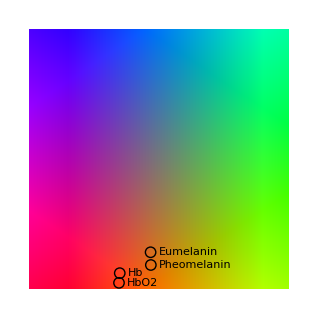
```mathematica
imgs={-Graphics-};
```

```mathematica
Clear[uProbFun]
uProbFun=Table[ProbFun[colorSpaceRules[[i]]],{i,1,5}];
```

```mathematica
uProbFun[[1]]
```

{Function[{pxl$60437},Chop[ⅇ^(-14.1379 (-0.5+pxl$60437⟦2⟧)^2-14.1379 (-0.5+pxl$60437⟦3⟧)^2)]],Function[{pxl$60437},Chop[ⅇ^(-0.00435146 (-57/2+pxl$60437⟦2⟧)^2-0.024545 (-12+pxl$60437⟦3⟧)^2)]]}

```mathematica
imgSmallLCaCbData=Table[processImage[ImageData[imgs[[j]],"Byte"],{},{uProbFun[[i,1]]},colorSpaceRules[[i]]],{j,1,Length[imgs]},{i,1,5}];
```

```mathematica
Dimensions[imgSmallLCaCbData]
```

{1,5,480,512,4}

```mathematica
SetAlphaChannel[imgs[[1]],Image[imgSmallLCaCbData[[1,5,All,All,4]]]]
```

-Graphics-

```mathematica
Image[imgSmallLCaCbData[[1,5,All,All]],ColorSpace->"RGB"]
```

-Graphics-

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
GraphicsGrid[Table[Column[{Image[imgSmallLCaCbData[[j,i,All,All]],ColorSpace->"RGB"],Row[{"  ",label[[j]],"  ",i,"σ"}]}],{j,1,3},{i,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
GraphicsGrid[Table[Column[{Image[imgSmallLCaCbData[[j,i,All,All,4]]],Row[{"  ",label[[j]],"  ",i,"σ"}]}],{j,1,3},{i,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

```mathematica
Block[{label},
label={"FSkin","JSkin","NSkin"};
GraphicsGrid[Table[Column[{SetAlphaChannel[imgs[[j]],Image[imgSmallLCaCbData[[j,i,All,All,4]]]],Row[{"  ",label[[j]],"  ",i,"σ"}]}],{j,1,3},{i,1,5}],Frame->All,Spacings->{0, 0},Alignment->{Center,Top}]
]
```

#### The Probability Function

After Redistribution we have two new spaces in which to express the stats parameters. The 0-dstMax range and the new 0-1 range where 0 and 1 correspond to different positions in the original unit space becase of the contraction of the information. The mean values are at the half way point in both

```mathematica
cd=dstMax/2
μd={0.5,0.5,0.5}
```

{257/2,57/2,12}

{0.5,0.5,0.5}

the standard deviations are scaled by the regions which are kept and the new ranges.

```mathematica
sd=dstMax s/(Λ[[All,2]]-Λ[[All,1]])
σd=σ/(λ[[All,2]]-λ[[All,1]])
```

{777.151,10.7193,4.5134}

{3.02394,0.188058,0.188058}

The probability is the product of these two Gaussians

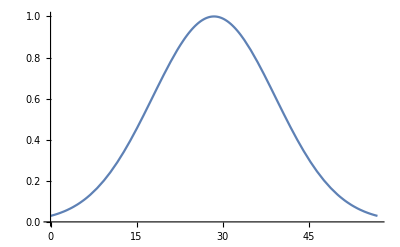
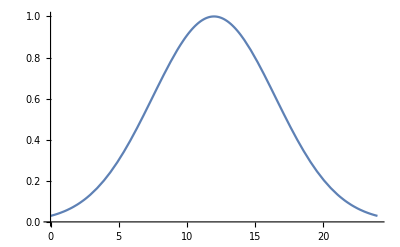

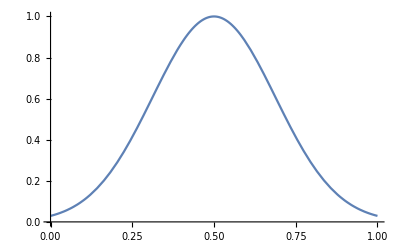
-Graphics--Graphics-

```mathematica
Row[{Plot[Exp[-(x-dstMax[[2]]/2)^2/(2 (sd[[2]])^2)],{x,0,dstMax[[2]]}],
Plot[Exp[-(x-dstMax[[3]]/2)^2/(2 (sd[[3]])^2)],{x,0,dstMax[[3]]}]}]
Row[{Plot[Exp[-(x-1/2)^2/(2( σd[[2]])^2)],{x,0,1}],
Plot[Exp[-(x-1/2)^2/(  2 (σd[[3]])^2)],{x,0,1}]}]
```

```mathematica
Clear[ProbFun]
ProbFun[rules_]:=Module[{cd,μd,sd,σd,pxl},
cd=("dstMax"/.rules)/2;
μd={0.5,0.5,0.5};
sd=("dstMax"/.rules)  ("s"/.rules)/(("Λ"/.rules)[[All,2]]-("Λ"/.rules)[[All,1]]);
σd=("σ"/.rules)/(("λ"/.rules)[[All,2]]-("λ"/.rules)[[All,1]]);
Quiet[{Function[{"pxl"},Chop["fun"]]/.{"pxl"->pxl,"fun"->Exp[-(pxl[[2]]-μd[[2]])^2/(2( σd[[2]])^2)]  Exp[-(pxl[[3]]-μd[[3]])^2/(2 (σd[[3]])^2)]},
Function[{"pxl"},Chop["fun"]]/.{"pxl"->pxl,"fun"->Exp[-(pxl[[2]]-cd[[2]])^2/(2( sd[[2]])^2)]  Exp[-(pxl[[3]]-cd[[3]])^2/(2 (sd[[3]])^2)]}},{Part::partd,Function::flpar}] ]
```

```mathematica
Clear[pxl]
{uProbFun,probFun } =ProbFun[colorSpaceRules[[1]]];
```

### The Region Function

The region catagorization function is applied before the redistribution function.

#### The Unreliable region Function

First we need to define the regions which suffer from whiteout and blackout. We take the ends of the minor axis and find the WOBO path theoretically for these points.

```mathematica
minorAxisEnds={μ-{0,2 σ[[2]],2 σ[[3]]},μ+{0,-2 σ[[2]],2 σ[[3]]}}
mAEPath1=WOBOPathLCaCb[minorAxisEnds[[1]]]
mAEPath2=WOBOPathLCaCb[minorAxisEnds[[2]]]
MMBO=({MapThread[Min,#],MapThread[Max,#]})&[{Sequence@@(({MapThread[Min,#],MapThread[Max,#]})&[(mAEPath1[[1;;3]])]),Sequence@@(({MapThread[Min,#],MapThread[Max,#]})&[(mAEPath2[[1;;3]])])}]
MMWO=({MapThread[Min,#],MapThread[Max,#]})&[{Sequence@@(({MapThread[Min,#],MapThread[Max,#]})&[(mAEPath1[[4;;6]])]),Sequence@@(({MapThread[Min,#],MapThread[Max,#]})&[(mAEPath2[[4;;6]])])}]
```

{{0.5,0.0955495,0.363732},{0.5,0.0955495,0.593883}}

{{0.,0.5,0.5},{0.0454227,0.525208,0.426908},{0.224211,0.442126,0.305374},{0.81976,0.442126,0.305374},{0.910606,0.416919,0.378466},{1.,0.5,0.5}}

{{0.,0.5,0.5},{0.0312944,0.453548,0.507812},{0.300928,0.328252,0.324524},{0.802594,0.328252,0.324524},{0.865183,0.374703,0.316712},{1.,0.5,0.5}}

{{0.,0.328252,0.305374},{0.300928,0.525208,0.507812}}

{{0.802594,0.328252,0.305374},{1.,0.5,0.5}}

The Limits in the unit space for unreliable WOBO values are

```mathematica
LWOBOLimits={MMBO[[2,1]],MMWO[[1,1]]}
CaWOBOLimits={Min[{MMBO[[1,2]],MMWO[[1,2]]}],Max[{MMBO[[2,2]],MMWO[[2,2]]}]}
CbWOBOLimits={Min[{MMBO[[1,3]],MMWO[[1,3]]}],Max[{MMBO[[2,3]],MMWO[[2,3]]}]}
Clear[L,Ca,Cb]
unreliableFun = Function[{L,Ca,Cb},Evaluate[(!(LWOBOLimits[[1]]<L<LWOBOLimits[[2]]))&&CaWOBOLimits[[1]]<Ca<CaWOBOLimits[[2]]&&CbWOBOLimits[[1]]<Cb<CbWOBOLimits[[2]]]]
```

{0.300928,0.802594}

{0.328252,0.525208}

{0.305374,0.507812}

Function[{L,Ca,Cb},!0.300928<L<0.802594&&0.328252<Ca<0.525208&&0.305374<Cb<0.507812]

```mathematica
Block[{L,WO,BO,RGBCubeRegion,LWOBOLimitsL,CaWOBOLimitsL,CbWOBOLimitsL,WORegion,BORegion,LCaCbTransform},
L=("L"/.colorSpaceRules[[1]]);
LWOBOLimitsL={MMBO[[1,1]],MMWO[[2,1]]}L[[1]];
CaWOBOLimitsL=(CaWOBOLimits-{1/2,1/2})L[[2]];
CbWOBOLimitsL=(CbWOBOLimits-{1/2,1/2})L[[3]];
WORegion = Cuboid[{LWOBOLimits[[1]],CaWOBOLimitsL[[1]],CbWOBOLimitsL[[1]]},{L[[1]],CaWOBOLimitsL[[2]],CbWOBOLimitsL[[2]]}];
BORegion = Cuboid[{0,CaWOBOLimitsL[[1]],CbWOBOLimitsL[[1]]},{LWOBOLimits[[2]],CaWOBOLimitsL[[2]],CbWOBOLimitsL[[2]]}];
LCaCbTransform=Composition[RotationTransform[LCaCbθ,{1,0,0}],RotationTransform[-ArcTan[1/Sqrt[2]],{0,0,1}],RotationTransform[Pi/4,{0,1,0}]];
RGBCubeRegion=TransformedRegion[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform];
WO=RegionIntersection[WORegion,RGBCubeRegion];
BO=RegionIntersection[BORegion,RGBCubeRegion];

Row[{RegionPlot3D[{TransformedRegion[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform],WO,BO},PlotPoints->125,PlotRange->{{0,L[[1]]},{-L[[2]]/2,L[[2]]/2},{-L[[3]]/2,L[[3]]/2}},PlotStyle->{Directive[Yellow,Opacity[0.5]],Directive[White,Opacity[0.5]],Directive[Black,Opacity[0.5]]},Mesh->None,ViewVertical->{1,0,0}],
RegionPlot3D[{TransformedRegion[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform],WORegion,BORegion},PlotPoints->125,PlotRange->{{0,L[[1]]},{-L[[2]]/2,L[[2]]/2},{-L[[3]]/2,L[[3]]/2}},PlotStyle->{Directive[Yellow,Opacity[0.5]],Directive[White,Opacity[0.5]],Directive[Black,Opacity[0.5]]},Mesh->None,ViewVertical->{1,0,0}],
Graphics3D[{Directive[Yellow,Opacity[0.5]],GeometricTransformation[Cuboid[{0,0,0},{1,1,1}],LCaCbTransform],Directive[White,Opacity[0.5]],WORegion,Directive[Black,Opacity[0.5]],BORegion},ViewVertical->{1,0,0}]}]
]
```

-Graphics3D--Graphics3D--Graphics3D-

#### The Reliable Region Function

We now define a function which catagorizes a pixel value as reliable. There are two options a rectangular segnentation or an eliptical segmentation.

```mathematica
sig=1;
minorAxisEnds={μ-{0,0,sig σ[[3]]},μ+{0,0,sig σ[[3]]}}
majorAxisEnds={μ-{0,sig σ[[2]],0},μ+{0,sig σ[[2]],0}}
```

{{0.5,0.356556,0.42127},{0.5,0.356556,0.536345}}

{{0.5,0.226053,0.478808},{0.5,0.48706,0.478808}}

```mathematica
Clear[L,Ca,Cb]
reliableFunSquare = Function[{L,Ca,Cb},Evaluate[majorAxisEnds[[1,2]]<Ca<majorAxisEnds[[2,2]]&&minorAxisEnds[[1,3]]<Cb<minorAxisEnds[[2,3]]]]
```

Function[{L,Ca,Cb},0.0955495<Ca<0.617563&&0.363732<Cb<0.593883]

The Elliptical partitioning function

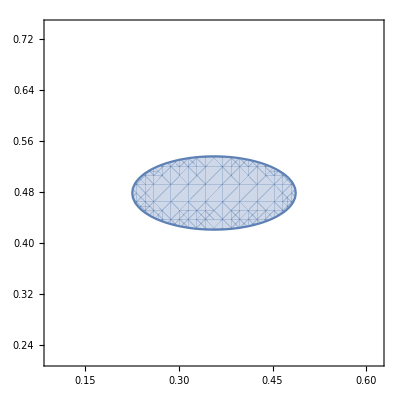

```mathematica
RegionPlot[(Ca-μ[[2]])^2/( σ[[2]])^2 + (Cb-μ[[3]])^2/( σ[[3]])^2<=1,{Ca,μ[[2]]-2 σ[[2]],μ[[2]]+2 σ[[2]]},{Cb,μ[[3]]-2 σ[[2]],μ[[3]]+2 σ[[2]]}]
```

#### The Region Function

```mathematica
regionFun = Function[{reliable,unreliable},FromDigits[Boole[{reliable,Xor[reliable,unreliable]}],2]]
```

Function[{reliable,unreliable},FromDigits[Boole[{reliable,reliable⊻unreliable}],2]]

The region Classifier

```mathematica
"qRsRange"/.colorSpaceRules[[1]]
```

{768,32640,32640}

```mathematica
Clear[ProbFun]
RegionClassifier[rules_,sig_:1]:=Module[{μ,σ,θ,qRsRange,minorAxisEnds,majorAxisEnds,mAEPath1,mAEPath2,chMM,MMBO,MMWO,LWOBOLimits,CaWOBOLimits,CbWOBOLimits,unreliableFun,reliableFunSquare,pts},
μ="μ"/.rules;
σ="σ"/.rules;
θ="θ"/.rules;
qRsRange=("qRsRange"/.colorSpaceRules[[1]]);
minorAxisEnds={μ-{0,0,sig σ[[3]]},μ+{0,0,sig σ[[3]]}};
majorAxisEnds={μ-{0,sig σ[[2]],0},μ+{0,sig σ[[2]],0}};

mAEPath1=WOBOPathLCaCb[minorAxisEnds[[1]],1,θ];
mAEPath2=WOBOPathLCaCb[minorAxisEnds[[2]],1,θ];
chMM=Function[{list},({MapThread[Min,list],MapThread[Max,list]})];
MMBO=chMM[{Sequence@@(chMM[(mAEPath1[[1;;3]])]),Sequence@@(chMM[(mAEPath2[[1;;3]])])}];
MMWO=chMM[{Sequence@@(chMM[(mAEPath1[[4;;6]])]),Sequence@@(chMM[(mAEPath2[[4;;6]])])}];
LWOBOLimits={MMBO[[2,1]],MMWO[[1,1]]};
CaWOBOLimits={Min[{MMBO[[1,2]],MMWO[[1,2]]}],Max[{MMBO[[2,2]],MMWO[[2,2]]}]};
CbWOBOLimits={Min[{MMBO[[1,3]],MMWO[[1,3]]}],Max[{MMBO[[2,3]],MMWO[[2,3]]}]};
unreliableFun = Function[{L,Ca,Cb},Evaluate[(!(qRsRange[[1]] LWOBOLimits[[1]]<L<qRsRange[[1]] LWOBOLimits[[2]]))&&qRsRange[[2]] CaWOBOLimits[[1]]<Ca<qRsRange[[2]] CaWOBOLimits[[2]]&&qRsRange[[3]] CbWOBOLimits[[1]]<Cb<qRsRange[[3]] CbWOBOLimits[[2]]]];
reliableFunSquare = Function[{L,Ca,Cb},Evaluate[qRsRange[[2]] majorAxisEnds[[1,2]]<Ca<qRsRange[[2]] majorAxisEnds[[2,2]]&&qRsRange[[3]] minorAxisEnds[[1,3]]<Cb<qRsRange[[3]] minorAxisEnds[[2,3]]]];
Function[{L,Ca,Cb},Evaluate[regionFun[reliableFunSquare[L,Ca,Cb],unreliableFun[L,Ca,Cb]]]]
]
```

```mathematica
rgnClassFun=RegionClassifier[colorSpaceRules[[1]],1]
rgnClass[pts_List]:=rgnClassFun[Sequence@@pts]
```

Function[{L$,Ca$,Cb$},2 Boole[10786.1<Ca$<12489.9&&15252.7<Cb$<16003.9]+Boole[(10786.1<Ca$<12489.9&&15252.7<Cb$<16003.9)⊻(!70.9638<L$<722.907&&14967.5<Ca$<16517.4&&14109.4<Cb$<16320.)]]

### Results

```mathematica
Max[imgSmallLCaCbDataClassified[[All,All,1;;3]]]
```

1.

```mathematica
Dimensions[imgSmallLCaCbDataClassified]
```

{3,5,2,306,408}

```mathematica
Image[imgSmallLCaCbDataClassified[[2,1,2,All,All,1;;3]]]
```

-Graphics-

```mathematica
"dstMax"/.colorSpaceRules[[1]]
```

{257,57,24}

```mathematica
"fSs"/.colorSpaceRules[[1]]
```

{1,-1,1}

```mathematica
Max[ImageData[imgs[[2]],"Byte"]]
```

255

```mathematica
("qRsRange"/.colorSpaceRules[[1]])
```

{768,32640,32640}

```mathematica
Round[imgSmallLCaCbDataClassified[[2,1,83,303,1;;3]]("qRsRange"/.colorSpaceRules[[1]])]
```

{654,26341,20400}

```mathematica
reliableFunSquare[Sequence@@(imgSmallLCaCbDataClassified[[2,1,62,315,1;;3]])]
```

False

```mathematica
imgSmallLCaCbDataClassified[[2,1,1,62,315,1;;3]]
```

{678,13584,16254}

```mathematica
regionClassifier[{678,13584,16254}]
```

3

```mathematica
imgSmallLCaCbDataClassified[[2,1,62,315,1;;3]]
regionClassifier[{654,26341,20400}]
```

{0.883268,0.929825,0.791667}

0

```mathematica
imgSmallLCaCbDataClassified=processImage[ImageData[imgs[[1]],"Byte"],{rgnClass},{rgnClass},colorSpaceRules[[1]]];
```

```mathematica
imgClass=imgSmallLCaCbDataClassified[[All,All,4]];
```

```mathematica
imgClassColor=imgClass/. {0->Black,1->Red,2->Blue,3->Green};
```

```mathematica
Position[imgSmallLCaCbDataClassified[[2,1,All,All,4]],1]
```

{}

```mathematica
Dimensions[imgSmallLCaCbDataClassified]
```

{318,319,4}

```mathematica
GraphicsRow[{Image[imgSmallLCaCbDataClassified[[All,All,1;;3]]],Image[imgSmallLCaCbDataClassified[[All,All,4]]/. {0->Black,1->Red,2->Blue,3->Green}]}]
```

-Graphics-

```mathematica
imgSmallLCaCbDataClassified[[1,1,10;;20,10;;20,4]]
```

Part::take: Cannot take positions 10 through 20 in {0.996109, 1., 0.833333, 0}.

{{{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0},309,{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0},{0.996109,1.,0.833333,0}},{1},314,{1},{1}}⟦1,3,4⟧
 |  |  |  |

```mathematica
Dimensions[imgSmallLCaCbDataClassified]
```

{318,319,4}

```mathematica
Image[imgSmallLCaCbDataClassified[[10;;200,10;;200,1;;3]]]
```

-Graphics-

```mathematica
Position[imgSmallLCaCbDataClassified[[All,All,1;;3]],n_/;!NumberQ[#]&]
```

{}

```mathematica
Max[imgSmallLCaCbDataClassified[[All,All,1;;3]]]
```

1.

```mathematica
imgSmallLCaCbDataClassified=Table[processImage[ImageData[imgs[[j]],"Byte"],{regionClassifier},{},colorSpaceRules[[i]]],{j,1,3},{i,1,5}];
```

## Junk

```mathematica
Clear[L,Ca,Cb]
reliableFunElliptical = Function[{L,Ca,Cb},Evaluate[(Ca-μ[[2]])^2/( σ[[2]])^2 + (Cb-μ[[3]])^2/( σ[[3]])^2<=1]]
```

```mathematica
{toLCaCb, fromLCaCb}=setLCaCb[LCaCbθ];
```

```mathematica
μRGB=fromLCaCb[c/255]
cRGB=255  μRGB
WOBOLimits=WOBOPathLCaCb[μRGB][[3;;4,1]]
qRsRange="qRsRange"/.colorSpaceRules[[2]];
unreliableFun=Function[{pxl},If[(pxl[[1]]<qRsRange[[2]] WOBOLimits[[1]]|| pxl[[1]]>qRsRange[[3]] WOBOLimits[[2]])&&pxl[[2]]<128,1,0]]
```

{0.451975,0.362291,0.685735}

{115.254,92.3841,174.862}

{0.137709,0.814265}

Function[{pxl},If[(pxl⟦1⟧<255 WOBOLimits⟦1⟧||pxl⟦1⟧>255 WOBOLimits⟦2⟧)&&pxl⟦2⟧<128,1,0]]

```mathematica
Clear[pxl]
path=WOBOPathLCaCb[μRGB]
pathMax=MapThread[Max,path]
pathMin=MapThread[Min,path]
WOBOLimits=path[[3;;4,1]]
unreliableFun=Function[{pxl},Evaluate[(pxl[[1]]<qRsRange[[1]] WOBOLimits[[1]] ||pxl[[1]]>qRsRange[[1]] WOBOLimits[[2]]) && (qRsRange[[2]] pathMin[[2]]<=pxl[[2]]≤ qRsRange[[2]] pathMax[[2]])&&(qRsRange[[3]] pathMin[[3]]<=pxl[[3]]≤ qRsRange[[3]] pathMax[[3]])]]
probFun=Function[{Ca,Cb,CaMin,CaMax,CbMin,CbMax},
1/2-Sqrt[(((Ca-CaMin)/(CaMax-CaMin)-1/2 )^2 +((Cb-CbMin)/(CbMax-CbMin)-1/2)^2)]
];
```

{{0.,0.5,0.5},{0.0779201,0.38434,0.51945},{0.137709,0.356556,0.478808},{0.814265,0.356556,0.478808},{0.970105,0.472216,0.459357},{1.,0.5,0.5}}

{1.,0.5,0.51945}

{0.,0.356556,0.459357}

{0.137709,0.814265}

Part::partd: Part specification pxl ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification pxl ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Function[{pxl},(pxl⟦1⟧<105.761||pxl⟦1⟧>625.356)&&11638.≤pxl⟦2⟧≤16320.&&14993.4≤pxl⟦3⟧≤16954.9]

```mathematica
pxl
```

{41,141,117}

```mathematica
path[[3;;4,1]]
```

{0.137709,0.814265}

```mathematica
qRsRange
```

{768,32640,32640}

```mathematica
qRsRange WOBOLimits[[1]]
```

{105.761,4494.84,4494.84}

```mathematica
MapThread[Less,{{0.5,0.2,0.3},{0.6,0.3,0.4}}]
```

{True,True,True}

```mathematica
μRGB=fromLCaCb[c/255]
cRGB=255  μRGB
WOBOLimits=WOBOPathLCaCb[μRGB][[3;;4,1]]
unreliableFun=Function[{pxl},If[(pxl[[1]]<255 WOBOLimits[[1]]|| pxl[[1]]>255 WOBOLimits[[2]])&&pxl[[2]]<128,1,0]]
```

{0.451975,0.362291,0.685735}

{115.254,92.3841,174.862}

{0.137709,0.814265}

Function[{pxl},If[(pxl⟦1⟧<255 WOBOLimits⟦1⟧||pxl⟦1⟧>255 WOBOLimits⟦2⟧)&&pxl⟦2⟧<128,1,0]]

```mathematica
imgData=ImageData[imgSmall,"Byte"];
```

```mathematica
probFun=Function[{Ca,Cb,CaMin,CaMax,CbMin,CbMax},
1/2-Max[Abs[({(Ca-CaMin)/(CaMax-CaMin)-1/2 ,(Cb-CbMin)/(CbMax-CbMin)-1/2})]]
];
```

```mathematica
probFun[Ca,Cb,0,CaMax,CbMin,CbMax]
```

1/2-Max[Abs[-1/2+Ca/CaMax],Abs[-1/2+(Cb-CbMin)/(CbMax-CbMin)]]

```mathematica
FullSimplify[1/2-Max[Abs[-1/2+(Ca-CaMin)/(CaMax-CaMin)],Abs[-1/2+(Cb-CbMin)/(CbMax-CbMin)]]]
```

1/2-Max[1/2 Abs[(-2 Ca+CaMax+CaMin)/(CaMax-CaMin)],1/2 Abs[(-2 Cb+CbMax+CbMin)/(CbMax-CbMin)]]

```mathematica
unreliableFun
```

Function[{pxl},pxl⟦1⟧<255 WOBOLimits⟦1⟧||pxl⟦1⟧>255 WOBOLimits⟦2⟧]

```mathematica
BinaryNumberSigned[num_,digits_]:=NumberForm[BaseForm[num,2],digits-1,DigitBlock->4,NumberPadding->{"0","0"},SignPadding->True,NumberSigns->{"-","+"}];
```

```mathematica
BinaryNumberSigned[2^(-2+8)-2^(-2+2 8),16]
```

(-011,1111,1100,0000)_2

```mathematica
qRsMax=Expand[{0, 2^(n-2) (2^n-1),2^(n-2) (2^n-1)}];
MatrixForm[qRsMax]
```

(0
-2^(-2+n)+2^(-2+2 n)
-2^(-2+n)+2^(-2+2 n))

```mathematica
2^{2 n-2}-2^{n-2}-(2^(-2+n)-2^(-2+2 n))
```

{-2^(-1+n)+2^(-1+2 n)}

```mathematica
Expand[2 2^(n-2) (2^n-1)]
```

-2^(-1+n)+2^(-1+2 n)

```mathematica
Block[{n=8},

δ=("δ"/.distroRules);
K=("K"/.distroRules);
L="L"/.distroRules;
λ="λ"/.distroRules;
ωp="ωp"/.distroRules;
qRsMin={0,- 2^(n-2) (2^n-1),- 2^(n-2) (2^n-1)};
qRsMax={0, 2^(n-2) (2^n-1),2^(n-2) (2^n-1)};
qRsRange={3 2^n,2 2^(n-2) (2^n-1),2 2^(n-2) (2^n-1)};
Λ=Round[2^n λ]; Λq=Round[qRsRange λ];
Ωp=Round[2^n λ]; Ωpq=Round[qRsRange λ];
Qdisc=Map[(2^3/2^n<#)&,({1,1,1}-λ[[All,2]]+λ[[All,1]])];
Qdist=Map[(2^3/2^n<#)&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])];
Qkeep=Map[(1/2^n<#)&,(ωp[[All,2]]-ωp[[All,1]])];
S=MapThread[Min,{δ K,N[L]}] {1/3,2^(1-n),2^(1-n)};
dstMax=Table[Round[disFun[[i]][qRsRange[[i]]]],{i,1,3}];


Column[{Grid[{{Row[{"θ = ",Θ+δθ," ≃ ",(2 π)/7}],SpanFromLeft,SpanFromLeft},{TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ","θ"," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA["47",8],Θ +thetaExtremaB["43",8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA["49",8],Θ +thetaExtremaB["45",8]}]}]],
TraditionalForm[Row[{Column[{Θ +thetaExtremaA[47,8],Θ +thetaExtremaB[43,8]}]," < ",Rationalize[LCaCbθ/Pi,N[1/(2 256)]]Pi," < ",Column[{Θ +thetaExtremaA[49,8],Θ +thetaExtremaB[45,8]}]}]]
}},Spacings->2,Frame->All,Alignment->Left],
Row[{"dstMax = ",MatrixForm@dstMax}],
Row[{qR["2 π"]," = ",MatrixForm[qR[(2 π)/7]]}],
Row[{fSs["2 π"]," = ",MatrixForm[fSs[(2 π)/7]]}],
Row[{"S = ",MatrixForm[S]}],
Row[{2^n Subscript["Q", "discard"]," = ",MatrixForm[Round[2^n ({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "distribute"]," = ",MatrixForm[Round[2^n(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{2^n Subscript["Q", "keep"]," = ",MatrixForm[Round[2^n(ωp[[All,2]]-ωp[[All,1]])]]}],
Row[{ Subscript["τ", "discard"]," = ",2^3/2^n}],
Row[{Subscript["τ", "distribute"]," = ",2^3/2^n}],
Row[{Subscript["τ", "keep"]," = ",1/2^n}],
Row[{ Subscript["Q", "discard"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,({1,1,1}-λ[[All,2]]+λ[[All,1]])]]}],
Row[{Subscript["Q", "distribute"]," = ",MatrixForm[Map[(Row[{2^3/2^n," < ",#}] )&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]," = ",MatrixForm[Map[(2^3/2^n<#)&,(λ[[All,2]]-ωp[[All,2]]+ωp[[All,1]]-λ[[All,1]])]]}],
Row[{Subscript["Q", "keep"]," = ",MatrixForm[Map[(Row[{1/2^n," < ",#}] )&,(ωp[[All,2]]-ωp[[All,1]])]]," = ",MatrixForm[Map[(1/2^n<#)&,(ωp[[All,2]]-ωp[[All,1]])]]}],
Grid[{{"","0-1","0-255","qRange"},{"λ",MatrixForm@λ,MatrixForm@Λ,MatrixForm@Λq},{"ω",MatrixForm@ωp,MatrixForm@Ωp,MatrixForm@Ωpq}}]
}]
]
```

θ = 0.902577 ≃ (2 π)/7 |  | 
(ϕ^o)_a(TraditionalForm`"47", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"43", TraditionalForm`8)+π/6 < θ < (ϕ^o)_a(TraditionalForm`"49", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"45", TraditionalForm`8)+π/6 | (ϕ^o)_a(TraditionalForm`"47", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"43", TraditionalForm`8)+π/6 < (2 π)/7 < (ϕ^o)_a(TraditionalForm`"49", TraditionalForm`8)+π/6
(ϕ^o)_b(TraditionalForm`"45", TraditionalForm`8)+π/6 | π/6+tan^-1((47 √3)/209)
π/6+tan^-1(43/(64 √3)) < (2 π)/7 < π/6+tan^-1(49/(69 √3))
π/6+tan^-1((15 √3)/64)
dstMax = (257
57
24)
qR[2 π] = (1 | 1 | 1
64 | -40 | -24
-10 | -54 | 64)
fSs[2 π] = (1
-1
1)
S = (0.334877
0.0126246
0.0118525)
256 Q_discard = (2
220
240)
256 Q_distribute = (0
0
0)
256 Q_keep = (254
36
16)
τ_discard = 1/32
τ_distribute = 1/32
τ_keep = 1/256
Q_discard = (1/32 < 0.0079153
1/32 < 0.86121
1/32 < 0.938808) = (False
True
True)
Q_distribute = (1/32 < 0.
1/32 < 0.
1/32 < 0.) = (False
False
False)
Q_keep = (1/256 < 0.992085
1/256 < 0.13879
1/256 < 0.0611915) = (True
True
True)
 | 0-1 | 0-255 | qRange
λ | (0.00395765 | 0.996042
0.287161 | 0.425951
0.448212 | 0.509403) | (1 | 255
74 | 109
115 | 130) | (3 | 765
9373 | 13903
14630 | 16627)
ω | (0.00395765 | 0.996042
0.287161 | 0.425951
0.448212 | 0.509403) | (1 | 255
74 | 109
115 | 130) | (3 | 765
9373 | 13903
14630 | 16627)

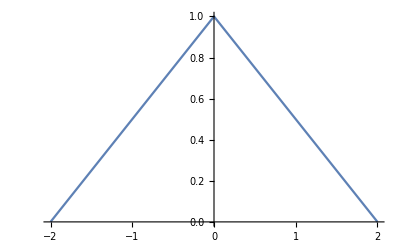

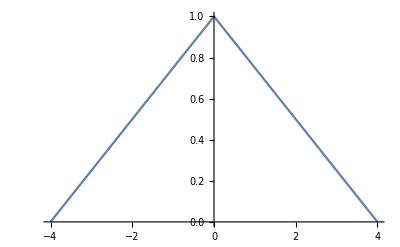

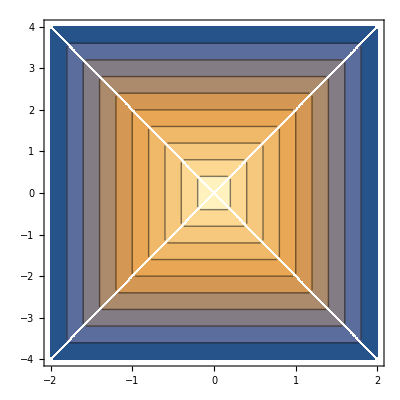

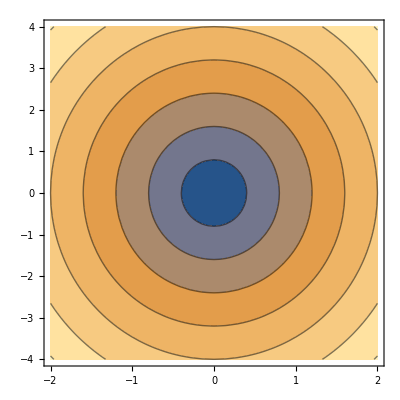

```mathematica
Plot[(1-1/2Abs[x]),{x,-2,2}]
Plot[(1-1/4Abs[y]),{y,-4,4}]
ContourPlot[Min[(1-1/2Abs[x]),(1-1/4Abs[y])],{x,-2,2},{y,-4,4}]
ContourPlot[Sqrt[(1/2Abs[x])^2+(1/4Abs[y])^2],{x,-2,2},{y,-4,4}]
```